# Modified GUPs

A clean worksheet for Calc17. And extended for corrected compations in Calc18, until Aug 29. 2014.

This worksheet is documented in a german-english fashion :)  It covers the complete discussion starting from the T00-Integral solving until temperature calculations. In the later parts, most computations are done (or at least supported) by numerical predictions. Much code is not so well documented, just ask me for details.

-- Sven Koeppel @ FIAS.

```mathematica
(* Die neue Wahl *)
V[q_, n_] = 1/(1 + q^(n+2))

(* Die alte Wahl *)
(*V[q_, n_] = 1/(1 + q^2)*)
vSide[q_,n_, side_]:= q^(1+n) * If[side>0,V[q,n],(-1)^n V[-q,n]] 
vEff[q_,n_] = vSide[q,n,+1]HeavisideTheta[q] + vSide[q,n,-1]HeavisideTheta[-q]
```

1/(1+q^(2+n))

((-1)^n q^(1+n) HeavisideTheta[-q])/(1+(-q)^(2+n))+(q^(1+n) HeavisideTheta[q])/(1+q^(2+n))

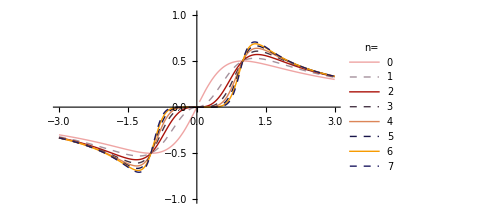

```mathematica
Plot[Table[vEff[q,n], {n,0,7}]//Evaluate,
{q,-3,3},
PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),
PlotLegends-> LineLegend[Table[n,{n,0,7}],LegendLabel-> "n="],
PlotRange-> {-1,1},
ImageSize-> Medium]
```

## Polstellen extrahieren

Code zwar zusammenkopiert, aber drübergeschaut.

```mathematica
ReduceToSolutions[reduceResult_, extractVariable_] := Cases[reduceResult,Equal[extractVariable, value_]-> value, 100]
polReduce[n_, side_] := Reduce[Denominator@vSide[q,n, side]==0,q]
polstellenSide[n_,side_] := polReduce[n,side]~ ReduceToSolutions ~ q
polstellen[n_] := Join@@(Select[polstellenSide[n,#[[1]]], #[[2]]]&) /@ {
+1 ->  (Re[#] ≥ 0&),
-1 -> (Re[#] ≤ 0&)
}
mitgenommenePolstellen[n_] := Select[polstellen[n], Im[#]≥ 0&]
```

```mathematica
(* Zeichne die Polstellen.
Diese Funktion/Zelle ist aus Polstellen.nb kopiert und etwas modifiziert. *)
Daten[n_] :={
{Re[#], Im[#]} & /@ (Solve[z^(2+n) == 1,z] /. {{z-> a_}-> a}) , (* in Blau *)
{Re[#], Im[#]} & /@ polstellenSide[n, +1],
{Re[#], Im[#]} & /@ polstellenSide[n, -1],
{Re[#], Im[#]} & /@ polstellen[n] (* schwarz *),
{Re[#], Im[#]} & /@ mitgenommenePolstellen[n]
}
MakePlot[n_,
label_:"Left and right hand poles"
] :=Show[ListPlot[
Daten[n],
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
FrameLabel->{{Im,None},{Re,label }},
PlotMarkers -> {
{Graphics[{Lighter@Blue, Opacity[0.3],Disk[]}], 0.05},
{
Graphics@{Darker@Yellow,
Circle[],
Disk[{0,0},1,{-Pi/2,Pi/2}],
Text[Style["R","Title",15,Bold,Darker@Darker@Brown], {+0.5, Center}]},
 0.1},
{
Graphics@{Lighter@Magenta,
Circle[],
Disk[{0,0},1,{Pi/2,3/2*Pi}],
Text[Style["L","Title",15,Bold,Darker[Magenta]], {-0.5, Center}]},
 0.1},
{Graphics[{Black,Thickness[0.15],Circle[]}],0.12},
{Graphics[{Red,Thickness[0.15],Circle[]}],0.18}
},
PlotRange-> All,
ImageSize->Medium],
Graphics[{Opacity[0.2],Circle[{0,0},1]}]
];
Manipulate[Show[
MakePlot[n],
Graphics[{Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{120,130},{0,0}]](*,
Text[Style[StringForm["# Residuen=``",ResidueList[n]//Length],{Black, 20}], Offset[{+30,-30},{0,0}]]*)}
]]
,{n,0,15,1}]
```

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# unique poles", "# poles","Unique Poles"}},
Table[{n,
Length@Union@polstellen[n],
Length@polstellen[n],
Union@polstellen[n] // Sort
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # unique poles | # poles | Unique Poles
0 | 2 | 4 | {-ⅈ,ⅈ}
1 | 4 | 4 | {-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)}
2 | 4 | 4 | {-(-1)^(1/4),(-1)^(1/4),-(-1)^(3/4),(-1)^(3/4)}
3 | 4 | 4 | {-(-1)^(1/5),(-1)^(1/5),-(-1)^(4/5),(-1)^(4/5)}
4 | 6 | 8 | {-ⅈ,ⅈ,-(-1)^(1/6),(-1)^(1/6),-(-1)^(5/6),(-1)^(5/6)}
5 | 8 | 8 | {-(-1)^(1/7),(-1)^(1/7),-(-1)^(3/7),(-1)^(3/7),-(-1)^(4/7),(-1)^(4/7),-(-1)^(6/7),(-1)^(6/7)}
6 | 8 | 8 | {-(-1)^(1/8),(-1)^(1/8),-(-1)^(3/8),(-1)^(3/8),-(-1)^(5/8),(-1)^(5/8),-(-1)^(7/8),(-1)^(7/8)}
7 | 8 | 8 | {-(-1)^(1/9),(-1)^(1/9),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(8/9),(-1)^(8/9)}

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "interesting poles"}},
Table[{n,
Length@Select[Arg@mitgenommenePolstellen[n],#≤ π/2&],
Select[Arg@mitgenommenePolstellen[n],#≤ π/2&]
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | interesting poles | 
0 | 2 | {π/2,π/2}
1 | 1 | {π/3}
2 | 1 | {π/4}
3 | 1 | {π/5}
4 | 3 | {π/2,π/6,π/2}
5 | 2 | {π/7,(3 π)/7}
6 | 2 | {π/8,(3 π)/8}
7 | 2 | {π/9,π/3}

## Integralberechnung

Achtung wegen der Vorfaktoren:
* Die Integralresiduenliste beinhaltet die kompletten Residuen, also auch den res f_± = 1/(2+n)-Fakt.
*  AValue beinhaltet den 1/(-2 i z)-Faktor und damit einen Teil von f_0. Grund: AValue[0] wird so sehr einfach.

```mathematica
IntegralResidueList[n_] := 
(2 Pi I) * (+1)  * Residue[vSide[q, n, Sign@Re@#] * Exp[+I q z], {q,#}]& /@ mitgenommenePolstellen[n]
IntegralValue[n_] := Total@IntegralResidueList[n]
AValue[n_] :=  - I/(2z)  * IntegralValue[n]
```

```mathematica
Grid[Table[{
n,
Grid[{mitgenommenePolstellen[n]}, Frame-> All],
Grid[{IntegralResidueList[n] / (2 Pi I)},Frame-> All]
},{n,0,7}], Frame-> All, Alignment-> {Left,Left}]
```

0 | ⅈ | ⅈ | ⅇ^-z/2 | ⅇ^-z/2
1 | (-1)^(1/3) | (-1)^(2/3) | 1/3 ⅇ^((-1)^(5/6) z) | 1/3 ⅇ^(-(-1)^(1/6) z)
2 | (-1)^(1/4) | (-1)^(3/4) | 1/4 ⅇ^((-1)^(3/4) z) | 1/4 ⅇ^(-(-1)^(1/4) z)
3 | (-1)^(1/5) | (-1)^(4/5) | 1/5 ⅇ^((-1)^(7/10) z) | 1/5 ⅇ^(-(-1)^(3/10) z)
4 | ⅈ | (-1)^(1/6) | ⅈ | (-1)^(5/6) | ⅇ^-z/6 | 1/6 ⅇ^((-1)^(2/3) z) | ⅇ^-z/6 | 1/6 ⅇ^(-(-1)^(1/3) z)
5 | (-1)^(1/7) | (-1)^(3/7) | (-1)^(4/7) | (-1)^(6/7) | 1/7 ⅇ^((-1)^(9/14) z) | 1/7 ⅇ^((-1)^(13/14) z) | 1/7 ⅇ^(-(-1)^(1/14) z) | 1/7 ⅇ^(-(-1)^(5/14) z)
6 | (-1)^(1/8) | (-1)^(3/8) | (-1)^(5/8) | (-1)^(7/8) | 1/8 ⅇ^((-1)^(5/8) z) | 1/8 ⅇ^((-1)^(7/8) z) | 1/8 ⅇ^(-(-1)^(1/8) z) | 1/8 ⅇ^(-(-1)^(3/8) z)
7 | (-1)^(1/9) | (-1)^(1/3) | (-1)^(2/3) | (-1)^(8/9) | 1/9 ⅇ^((-1)^(11/18) z) | 1/9 ⅇ^((-1)^(5/6) z) | 1/9 ⅇ^(-(-1)^(1/6) z) | 1/9 ⅇ^(-(-1)^(7/18) z)

“Herleitung” der obskuren Identität, mit der die E-Funktionen zugunsten Winkelfunktionen verschwinden:

```mathematica
Exp[I Exp[I φ] z] + Exp[-I Exp[- I φ] z] // ComplexExpand
```

2 ⅇ^(-z Sin[φ]) Cos[z Cos[φ]]

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# poles","Wert für A(p)"}},
Table[{n,
Length@mitgenommenePolstellen[n],
AValue[n] ,
AValue[n]//ComplexExpand 
(*AValue[n]//ComplexExpand // FullSimplify*)
},{n,0,8}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # poles | Wert für A(p) | 
0 | 2 | (ⅇ^-z π)/z | (ⅇ^-z π)/z
1 | 2 | -(ⅈ (2/3 ⅈ ⅇ^(-(-1)^(1/6) z) π+2/3 ⅈ ⅇ^((-1)^(5/6) z) π))/(2 z) | (2 ⅇ^(-(√3 z)/2) π Cos[z/2])/(3 z)
2 | 2 | -(ⅈ (1/2 ⅈ ⅇ^(-(-1)^(1/4) z) π+1/2 ⅈ ⅇ^((-1)^(3/4) z) π))/(2 z) | (ⅇ^(-z/(√2)) π Cos[z/(√2)])/(2 z)
3 | 2 | -(ⅈ (2/5 ⅈ ⅇ^(-(-1)^(3/10) z) π+2/5 ⅈ ⅇ^((-1)^(7/10) z) π))/(2 z) | (ⅇ^(-√(5/8-(√5)/8) z) π Cos[1/4 (-1-√5) z])/(5 z)+(ⅇ^(-√(5/8-(√5)/8) z) π Cos[1/4 (1+√5) z])/(5 z)+ⅈ ((ⅇ^(-√(5/8-(√5)/8) z) π Sin[1/4 (-1-√5) z])/(5 z)+(ⅇ^(-√(5/8-(√5)/8) z) π Sin[1/4 (1+√5) z])/(5 z))
4 | 4 | -(ⅈ (2/3 ⅈ ⅇ^-z π+1/3 ⅈ ⅇ^(-(-1)^(1/3) z) π+1/3 ⅈ ⅇ^((-1)^(2/3) z) π))/(2 z) | (ⅇ^-z π)/(3 z)+(ⅇ^(-z/2) π Cos[(√3 z)/2])/(3 z)
5 | 4 | -1/(2 z)ⅈ (2/7 ⅈ ⅇ^(-(-1)^(1/14) z) π+2/7 ⅈ ⅇ^(-(-1)^(5/14) z) π+2/7 ⅈ ⅇ^((-1)^(9/14) z) π+2/7 ⅈ ⅇ^((-1)^(13/14) z) π) | (2 ⅇ^(-z Sin[π/7]) π Cos[z Cos[π/7]])/(7 z)+(2 ⅇ^(-z Cos[π/14]) π Cos[z Sin[π/14]])/(7 z)
6 | 4 | -(ⅈ (1/4 ⅈ ⅇ^(-(-1)^(1/8) z) π+1/4 ⅈ ⅇ^(-(-1)^(3/8) z) π+1/4 ⅈ ⅇ^((-1)^(5/8) z) π+1/4 ⅈ ⅇ^((-1)^(7/8) z) π))/(2 z) | (ⅇ^(-z Sin[π/8]) π Cos[z Cos[π/8]])/(4 z)+(ⅇ^(-z Cos[π/8]) π Cos[z Sin[π/8]])/(4 z)
7 | 4 | -(ⅈ (2/9 ⅈ ⅇ^(-(-1)^(1/6) z) π+2/9 ⅈ ⅇ^(-(-1)^(7/18) z) π+2/9 ⅈ ⅇ^((-1)^(11/18) z) π+2/9 ⅈ ⅇ^((-1)^(5/6) z) π))/(2 z) | (2 ⅇ^(-(√3 z)/2) π Cos[z/2])/(9 z)+(2 ⅇ^(-z Sin[π/9]) π Cos[z Cos[π/9]])/(9 z)
8 | 6 | -1/(2 z)ⅈ (2/5 ⅈ ⅇ^-z π+1/5 ⅈ ⅇ^(-(-1)^(1/5) z) π+1/5 ⅈ ⅇ^(-(-1)^(2/5) z) π+1/5 ⅈ ⅇ^((-1)^(3/5) z) π+1/5 ⅈ ⅇ^((-1)^(4/5) z) π) | (ⅇ^-z π)/(5 z)+(ⅇ^(1/4 (-1-√5) z) π Cos[√(5/8-(√5)/8) z])/(5 z)+(ⅇ^(1/4 (1-√5) z) π Cos[√(5/8+(√5)/8) z])/(5 z)

Für das korrekte Ergebnis (𝒯^0)_0=f_0 A_value beinhaltet das f_0 in diesem Worksheet die restlichen Faktoren im Vergleich zum Paper

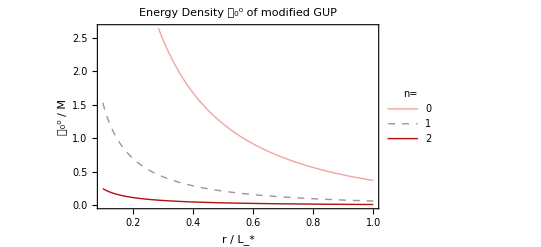

```mathematica
Ω[d_] := (2 Pi^((d+1)/2))/Gamma[(d+1)/2]
f0[n_] := Ω[n+2]/(2π)^(2+n)(* Echte Vorfaktoren, oben in AValue schon was Teile mitgenommen *)
Plot[Evaluate@Table[f0@n AValue@n, {n,0,2}], {z,0.1,1},
PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),
PlotLegends-> Placed[LineLegend[Table[n,{n,0,7}],
LegendLabel-> "n=", LegendLayout-> {"Row", 3}],{Right,Bottom}],
FrameLabel->{"r / L_*","𝒯_0^0 / M"},
PlotLabel-> "Energy Density 𝒯_0^0 of modified GUP",
Frame-> True(*,
PlotRange-> {-1,1}*)
]
```

Zur Berechnung von g_00 nutzen wir generische Lösung der Rizzo-DGL. Dabei wird an dieser Stelle hier das M reingemogelt, was dem physikalischen M/(M^(n+2))_* entspricht.

```mathematica
g00[n_, r_] :=1- M/r^(1+n)2/(n+2)Integrate[z^(n+2) f0[n]AValue[n],{z,0,r}]
g00s = Table[g00[n,r],{n,0,7}];
```

## Looking for the extremal radius

```mathematica
(* Prepare Export and metric units *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
```

```mathematica
(* Epic Epilog-Labels coming here, modified for the current problem:
   Featuring scaling and correct Inset (no rectangle nonrotated box).
 ASSUMING data be a list of X as variable, ideal for g00s. *)
ClearAll[EpiLabels]
EpiLabels[xpoint_, data_, labels_,axisratio_:1]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Inset[Rotate[Text[labels[[#]],Background -> White],
ArcTan@Re@N[(D[data⟦#⟧,X]/.{X-> xpoints⟦#⟧}) ] / axisratio] ,
{xpoints⟦#⟧, 0 +( data/.X-> xpoints⟦#⟧)⟦#⟧}
]& /@ Range@Length@data] (* 1: any value to introspect list*)

point[color_, coord_,size_:0.37] := Inset[
Graphics@{Opacity[0.9], color, Disk[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
coord, {0,0}, size
]
miniToSol[res_] := res /. {y_,{_ -> x_}} -> {x,y} (* for FindMinimum -> Coordinate  *)
rootToSol[res_] := res  /. {_ -> x_} -> x (* for first FindRoot -> value *)
```

### Find r_C and M_* numerically

```mathematica
(* find extremal Subscript[r, 0] Values. The test Masses are "experimental" *) 
r0s = First@Transpose@Table[miniToSol@FindMinimum[
Re@g00s⟦n+1⟧/.M-> 10 (n+1)^6, {r,1}
 ],{n,0,Length@g00s-1}];
(* fi3d extremal Mass values *)
Ms = Table[rootToSol@FindRoot[Re@g00s⟦n+1⟧/.r-> r0s⟦n+1⟧, {M,10^n}] ,{n,0,Length@g00s-1}];
Grid[{
{"n"}~Join~Range[0,Length@g00s-1],
{"r_0"}~Join~r0s,
{"M_*"}~Join~Ms
}, Frame-> All]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum :: lstol will be suppressed during this calculation.

n | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
r_0 | 1.79328 | 1.27534 | 1.07714 | 0.993701 | 1.01592 | 0.981144 | 0.953649 | 0.932502
M_* | 3.35092 | 53.0073 | 621.491 | 6536.7 | 35182.9 | 359680. | 3.69058×10^6 | 3.8323×10^7

```mathematica
%//TeXForm
```

\begin{array}{ccccccccc}
 \text{n} & 0 & 1 & 2 & 3 & 4 & 5 & 6 & 7 \\
 r_0 & 1.79328 & 1.27534 & 1.07714 & 0.993701 & 1.01592 & 0.981144 & 0.953649 & 0.932502 \\
 M_* & 3.35092 & 53.0073 & 621.491 & 6536.7 & 35182.9 & 359680. & 3.69058\times 10^6 &
   3.8323\times 10^7 \\
\end{array}

### Interactive Plot fuer variierende M, n.

```mathematica
getM[n_] := Ms⟦n+1⟧
Manipulate[
Plot[Evaluate@Re@({g00s⟦n+1⟧, 1-(2M)/((n+2)Ω[n])1/r^(1+n)}/.{M-> m}),
{r,0.03,10},
PlotRangePadding->0,
PlotStyle-> {Red, Blue},
Frame-> True,
FrameLabel->{"r / L","g_00"},
PlotRange-> {-1,1.7},
GridLines-> {{r0s⟦n+1⟧},{1}},
ImageSize-> Medium,
Epilog-> {point[Red,{r0s⟦n+1⟧,g00s⟦n+1⟧/.{r-> r0s⟦n+1⟧, M-> m}  }]},
PlotLabel-> "Metric g_00 of modified GUP in n="<>ToString@n<>
" LXDs\n r_0="<>ToString@r0s⟦n+1⟧ <> ", g00(r_0)=" <>ToString@Ms⟦n+1⟧
<>", M="<>ToString@m],
{{m,1},0.4,2getM[n]},{n,0,Length@g00s - 1,1}]
```

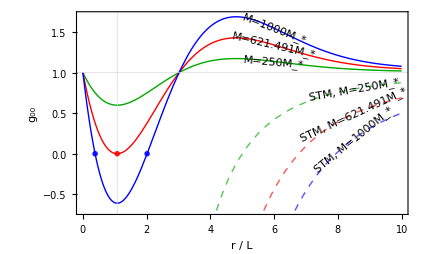

```mathematica
(* @Re@: Cut off small imaginary parts *)
fig =Module[{n=2,chosenM},
chosenM={250, Ms⟦n+1⟧,1000};
pointSize=0.15;
labels = "M="<>ToString@#<> "M_*"&/@chosenM ;
labelsSMM = "STM, "<>#&/@labels;
SMM = 1-(2M)/(n+2)1/r^(1+n);
Plot[Evaluate@Re@Flatten@Table[
{g00s⟦n+1⟧, SMM}/.{M-> M},{M,chosenM}], {r,0,10},
PlotRangePadding->0,
PlotStyle->Flatten[{#, {Dashed,Lighter@#}}&/@{Darker@Green, Red, Blue},1],
Frame-> True,
FrameLabel->{"r / L","g_00"},
PlotRange-> {-0.7,1.7},
Epilog-> {
EpiLabels[6,g00s⟦n+1⟧/.{M-> #,r-> X}&/@ chosenM,labels,5/10],
EpiLabels[8.5,SMM/.{M-> #, r-> X}&/@ chosenM,labelsSMM, 4.1/10],
point[Red,{r0s⟦n+1⟧,0},pointSize],
point[Blue, {rootToSol@FindRoot[Re@g00s⟦n+1⟧/. M-> Last@chosenM,{r,1}],0},pointSize],
point[Blue, {rootToSol@FindRoot[Re@g00s⟦n+1⟧/. M-> Last@chosenM,{r,2}],0},pointSize]
},
GridLines-> {{r0s⟦n+1⟧},{1}},
ImageSize -> 15cm,
AspectRatio-> 0.6
(* wird in Latex gemacht: *)
(*lotLabel-> "Metric component g_00 of modified GUP in n=2 LXDs"]*)
]]
```

```mathematica
Export["../../Master-Calc18/figures/g00-n2.pdf",fig]
```

../../Master-Calc18/figures/g00-n2.pdf

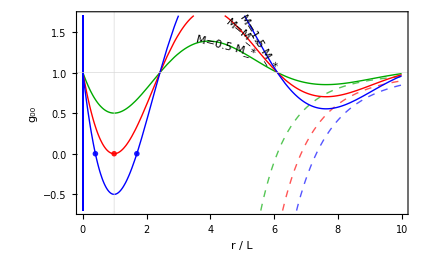

```mathematica
fig =Module[{n=5,chosenM},
chosenM={0.5Ms⟦n+1⟧, Ms⟦n+1⟧,1.5Ms⟦n+1⟧};
pointSize=0.15;
labels = {"M=0.5 M_*", "M=M_*", "M=1.5 M_*"};
SMM = 1-(2M)/(n+2)1/r^(1+n);
Plot[Evaluate@Re@Flatten@Table[
{g00s⟦n+1⟧, SMM}/.{M-> M},{M,chosenM}], {r,0,10},
PlotRangePadding->0,
PlotStyle->Flatten[{#, {Dashed,Lighter@#}}&/@{Darker@Green, Red, Blue},1],
Frame-> True,
FrameLabel->{"r / L","g_00"},
PlotRange-> {-0.7,1.7},
Epilog-> {
EpiLabels[{4.5,5.0, 5.5},g00s⟦n+1⟧/.{M-> #,r-> X}&/@ chosenM,labels,6/10],
point[Red,{r0s⟦n+1⟧,0},pointSize],
point[Blue, {rootToSol@FindRoot[Re@g00s⟦n+1⟧/. M-> Last@chosenM,{r,0.5}],0},pointSize],
point[Blue, {rootToSol@FindRoot[Re@g00s⟦n+1⟧/. M-> Last@chosenM,{r,2}],0},pointSize]
},
GridLines-> {{r0s⟦n+1⟧},{1}},
Exclusions-> Range[0,0.1], (* hat quasi keinen Effekt... sollte bloss senkrechte Striche bei r=0 unterbinden *)
ImageSize -> 15cm,
AspectRatio-> 0.6
(* Wird in Latex gemacht *)
(*PlotLabel-> "Metric component g_00 of modified GUP in n="<>ToString@n<>" LXDs"]*)
]]
```

```mathematica
Export["../../Master-Calc18/figures/g00-n5.pdf",fig]
```

../../Master-Calc18/figures/g00-n5.pdf

## Temperature

```mathematica
(* wg Simplify ca 10sec Laufzeit *)
Ts = 1/(4π M ) D[g00s,r] * Table[Ω[n+1], {n,0,Length@g00s-1}];
```

```mathematica
Off[FindMaximum::lstol]
TsMaxima =miniToSol@FindMaximum[Re@#,{r,2}]&/@Ts
```

{{3.38363,0.0202156},{2.51257,0.00655127},{2.26118,0.00166479},{2.18714,0.000309357},{2.19159,0.0000558368},{2.17113,6.97503×10^-6},{2.1577,7.76522×10^-7},{2.14889,7.74554×10^-8}}

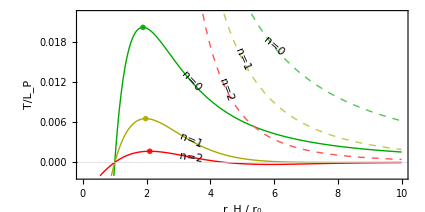

```mathematica
fig=Module[{chosenN},
chosenN = {0,1,2};
colors = {Darker@Green, Darker@Yellow, Red};
labels = "n="<>ToString@# &/@ chosenN;
TData = Table[Ts⟦n+1⟧ /. {r-> r * r0s⟦n+1⟧}, {n,chosenN}];
TSSM =  Table[D[1-2/(r^(1+n)),r] /. {r -> r r0s⟦n+1⟧}, {n, chosenN}];
Plot[Evaluate@Join@{Re@TData, TSSM},
{r,0,10},
PlotStyle-> Join[colors,{Dashed,Lighter@#}&/@colors],
PlotRangePadding -> None,
FrameLabel -> {"r_H / r_0", "T/L_P"},
Frame-> True,
Epilog-> Join[
{EpiLabels[3.4,TData/. r-> X,labels , 0.02/3]},
{EpiLabels[{6,5,4.5},TSSM/. r-> X,labels , 0.02/2.5]},
Inset[
Graphics@{Opacity[0.9], #⟦2⟧, Disk[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
{#⟦1,1⟧/#⟦3⟧,#⟦1,2⟧}, {0,0}, 0.17
]& /@ Transpose@{TsMaxima⟦chosenN+1⟧,colors, r0s⟦chosenN+1⟧}
],
PlotRange-> {-0.1Max@Last@Transpose@TsMaxima,1.1Max@Last@Transpose@TsMaxima},
GridLines-> {{},{0}},
AspectRatio -> 0.5,
ImageSize-> 15 cm
]
]
```

```mathematica
Export["../../Master-Calc18/figures/Temp.pdf",fig]
```

../../Master-Calc18/figures/Temp.pdf

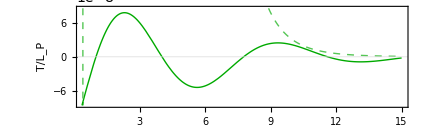

```mathematica
fig=Module[{chosenN},
chosenN = {7};
colors = {Darker@Green};
labels = "n="<>ToString@# &/@ chosenN;
TData = Table[Ts⟦n+1⟧ /. {r-> r * r0s⟦n+1⟧}, {n,chosenN}];
TSSM =  Table[D[1-2/(r^(1+n)),r] /. {r -> r r0s⟦n+1⟧}, {n, chosenN}];
Plot[Evaluate@Join@{Re@TData, TSSM},
{r,0.4,15},
PlotStyle-> Join[colors,{Dashed,Lighter@#}&/@colors],
PlotRangePadding -> None,
FrameLabel -> {"r_H / r_0", "T/L_P"},
Frame-> True,
PlotRange-> {-1.1Max@Last@Transpose@TsMaxima⟦chosenN+1⟧,1.1Max@Last@Transpose@TsMaxima⟦chosenN+1⟧},
GridLines-> {{},{0}},
AspectRatio -> 0.3,
Exclusions-> Range[0,0.1],
ImageSize-> 15 cm
]
]
```

```mathematica
Export["../../Master-Calc18/figures/Temp-n7.pdf",fig]
```

../../Master-Calc18/figures/Temp-n7.pdf